#### Homework

Calculate the value of  Calendar spread under the above market conditions

```mathematica
Subscript[𝕧, ϕ_,r_,𝔻_,σ_][τ_,x_]:=1/(2 √(π τ))ⅇ^(x(1/2-(r-𝔻)/σ^2)-(((4 r^2+4 r(σ^2-2𝔻)+(σ^2+2𝔻)^2)τ)/(4 σ^2))) Integrate[ⅇ^(-ξ (1/2-(r-𝔻)/σ^2)-(ξ-x)^2/(4τ))ϕ[ⅇ^ξ],{ξ,-∞,+∞},Assumptions-> τ>0]
```

```mathematica
Subscript[Vcall, k_,T_,σ_,r_,𝔻_][t_,S_]:=1/2 ⅇ^(r (t-T)) (ⅇ^((-t+T) (r-𝔻)) S (1+Erf[(-(t-T) (2 (r-𝔻)+σ^2)+2 Log[S/k])/(2 √2 √((-t+T) σ^2))])+k (-2+Erfc[(-(t-T) (2 (r-𝔻)-σ^2)+2 Log[S/k])/(2 √2 √((-t+T) σ^2))]))
```

```mathematica
Subscript[CallPayoff, K_][S_]:=Piecewise[{{0,S<K},{S-K,S>K}}]
```

```mathematica
Subscript[P, T_,r_,𝔻_,σ_,K_][t_,S_]:=Subscript[Vcall, K,T,σ,r,𝔻][t,S]
```

```mathematica
Subscript[CalendarSpreadPayoff, K_,T1_,T2_][S_]:=Subscript[P, T2-T1,r,𝔻,σ,K][T1,S]-Subscript[CallPayoff, K][S]
```

```mathematica
With[{T1=2013.9,T2=2014,σ=.3,r=.02,𝔻=0,K=50},
Plot[Subscript[CalendarSpreadPayoff, K,T1,T2][S],{S,30,70},Frame-> True,Axes-> False,AxesOrigin-> {40,0},
PlotStyle->{Thickness[.01],Red} ]]
```

-Graphics-

```mathematica
Subscript[CS, r_,𝔻_,σ_,K_,T1_,T2_][t_,S_]=Subscript[𝕧, Subscript[CalendarSpreadPayoff, K,T1,T2],r,𝔻,σ][τ,x]/.{τ->1/2(T-t)σ^2,x->Log[S]}//Simplify
```

𝕧_(CalendarSpreadPayoff_(K,T1,T2),r,𝔻,σ)[1/2 (-t+T) σ^2,Log[S]]

## Experiment with hedging

```mathematica
Subscript[SS, r_,T_,𝔻_,σ_][t_,S_]:=(ⅇ^(-1/8 (-t+T) (4 r^2+4 r (-2 𝔻+σ^2)+(2 𝔻+σ^2)^2)-((-2 r+2 𝔻+σ^2) (-(t-T) (2 r-2 𝔻-σ^2)+4 Log[S]))/(8 σ^2)) S^(1/2+(-r+𝔻)/σ^2) (60 r t Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2))-60 t 𝔻 Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2))-30 t σ^2 Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2))+60 Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] Log[30] √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2))-60 r T Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[900]-2 Log[S])^2)/((-t+T) σ^2))+60 T 𝔻 Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[900]-2 Log[S])^2)/((-t+T) σ^2))+30 T σ^2 Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[900]-2 Log[S])^2)/((-t+T) σ^2))+30 √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2)) √((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[900]-2 Log[S])^2)-2 ⅇ^(-(t-T) (r-𝔻)) r S t Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2))+2 ⅇ^(-(t-T) (r-𝔻)) S t 𝔻 Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2))-ⅇ^(-(t-T) (r-𝔻)) S t σ^2 Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2))-2 ⅇ^(-(t-T) (r-𝔻)) S Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] Log[30] √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2))-ⅇ^(-(t-T) (r-𝔻)) S √((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[900]-2 Log[S])^2) √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2))+2 ⅇ^(-(t-T) (r-𝔻)) r S T Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[900]-2 Log[S])^2)/((-t+T) σ^2))-2 ⅇ^(-(t-T) (r-𝔻)) S T 𝔻 Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[900]-2 Log[S])^2)/((-t+T) σ^2))+ⅇ^(-(t-T) (r-𝔻)) S T σ^2 Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[900]-2 Log[S])^2)/((-t+T) σ^2))-60 Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2)) Log[S]+2 ⅇ^(-(t-T) (r-𝔻)) S Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2)) Log[S]))/(2 √(-(t-T) σ^2) √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2)) √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[900]-2 Log[S])^2)/((t-T) σ^2)))+(ⅇ^(-1/8 (-t+T) (4 r^2+4 r (-2 𝔻+σ^2)+(2 𝔻+σ^2)^2)-((-2 r+2 𝔻+σ^2) (-(t-T) (2 r-2 𝔻-σ^2)+4 Log[S]))/(8 σ^2)) S^(1/2+(-r+𝔻)/σ^2) (80 r t Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2))-80 t 𝔻 Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2))-40 t σ^2 Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2))+80 Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] Log[40] √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2))-80 r T Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[1600]-2 Log[S])^2)/((-t+T) σ^2))+80 T 𝔻 Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[1600]-2 Log[S])^2)/((-t+T) σ^2))+40 T σ^2 Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[1600]-2 Log[S])^2)/((-t+T) σ^2))-40 √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2)) √((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[1600]-2 Log[S])^2)-2 ⅇ^(-(t-T) (r-𝔻)) r S t Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2))+2 ⅇ^(-(t-T) (r-𝔻)) S t 𝔻 Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2))-ⅇ^(-(t-T) (r-𝔻)) S t σ^2 Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2))-2 ⅇ^(-(t-T) (r-𝔻)) S Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] Log[40] √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2))+ⅇ^(-(t-T) (r-𝔻)) S √((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[1600]-2 Log[S])^2) √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2))+2 ⅇ^(-(t-T) (r-𝔻)) r S T Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[1600]-2 Log[S])^2)/((-t+T) σ^2))-2 ⅇ^(-(t-T) (r-𝔻)) S T 𝔻 Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[1600]-2 Log[S])^2)/((-t+T) σ^2))+ⅇ^(-(t-T) (r-𝔻)) S T σ^2 Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[1600]-2 Log[S])^2)/((-t+T) σ^2))-80 Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2)) Log[S]+2 ⅇ^(-(t-T) (r-𝔻)) S Erf[(√(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2)))/(2 √2)] √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2)) Log[S]))/(2 √(-(t-T) σ^2) √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻+t σ^2-T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2)) √(-((2 r (t-T)-2 t 𝔻+2 T 𝔻-t σ^2+T σ^2+Log[1600]-2 Log[S])^2)/((t-T) σ^2)));
```

```mathematica
With[{T=2014,σ=.25,r=.02,𝔻=.01},Subscript[SS, r,T,𝔻,σ][2013.8,50]]
```

10.1453

To see hedging in action, we shall simulate the stock(i.e., the underlying)dynamics

```mathematica
T=2014;σ=.25;r=.02;𝔻=.01;t0=2013.8;S0=50;K=1000;
𝕒=.15;
```

```mathematica
Subscript[SS, r,T,𝔻,σ][t0,S0]
```

10.1453

```mathematica
dt=(T-t0)/K//N
```

0.0002

```mathematica
dB=Table[Sqrt[dt]Random[NormalDistribution[]],{K}];
```

```mathematica
FF[{t_,S_},db_]:={t+dt,S+S 𝕒 dt+S σ db}
```

```mathematica
SList=FoldList[FF,{t0,S0},dB];
```

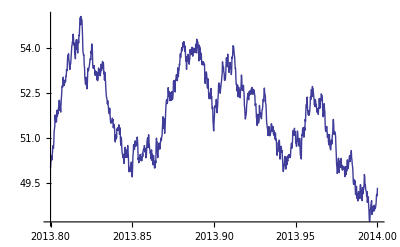

```mathematica
ListPlot[SList,Joined-> True]
```

```mathematica
Subscript[ss, r_,T_,𝔻_,σ_][{t_,S_}]:=Subscript[SS, r,T,𝔻,σ][t,S]
```

```mathematica
Subscript[SS, r,T,𝔻,σ][t0,S0]
```

10.1453

```mathematica
Subscript[ss, r,T,𝔻,σ][{t0,S0}]
```

10.1453

```mathematica
Subscript[ss, r,T,𝔻,σ][SList[[1]]]
```

10.1453

```mathematica
Off[General::unfl]
```

```mathematica
ssList=Subscript[ss, r,T,𝔻,σ]/@SList;
timeList =Transpose[SList][[1]];
```

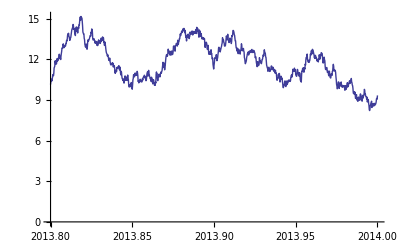

```mathematica
ListPlot[Transpose[{timeList,ssList}],Joined-> True]
```

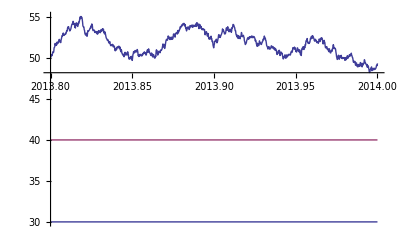

```mathematica
GraphicsGrid[{{Show[ListPlot[SList,Joined-> True],Plot[{30,40},{t,t0,T}],PlotRange->{0, All}]},{ListPlot[Transpose[{timeList,ssList}],Joined-> True]}}]
```

```mathematica
Off[General::unfl]
```

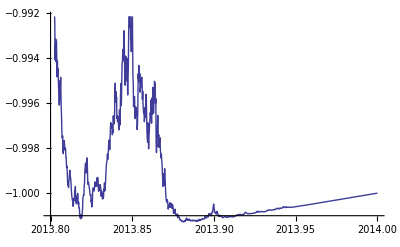

```mathematica
ListPlot[Transpose[{timeList,HedgeList=-Derivative[{0,1}][Subscript[ss, r,T,𝔻,σ]]/@SList}],Joined-> True]
```

```mathematica
Take[HedgeList,2]
```

{-0.983139,-0.984796}

```mathematica
Take[-Differences[HedgeList]Drop[Transpose[SList][[2]],1],2]
```

{0.0831823,0.0313171}

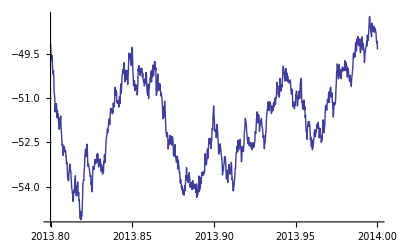

```mathematica
ListPlot[Transpose[
{timeList,HedgeValueList=-Derivative[{0,1}][Subscript[ss, r,T,𝔻,σ]][#]#[[2]]&/@SList}],Joined-> True]
```

```mathematica
HedgingCashInflux=-Differences[HedgeList]Drop[Transpose[SList][[2]],1];
```

```mathematica
DividendCashInflux=𝔻 Drop[HedgeList,1]Drop[Transpose[SList][[2]],1]dt;
```

```mathematica
CashFunction[PrevCash_,CashInflux_]:=PrevCash+r PrevCash dt+CashInflux
```

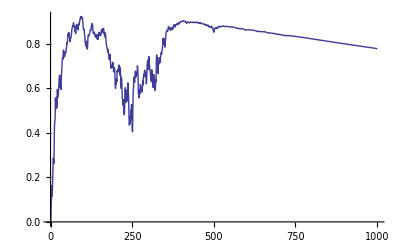

```mathematica
ListPlot[cashEvolustion=FoldList[CashFunction,0,HedgingCashInflux+DividendCashInflux],Joined-> True]
```

```mathematica
ListPlot[Transpose[{timeList,HedgeValueList=-Derivative[{0,1}][Subscript[ss, r,T,𝔻,σ]][#]#[[2]]&/@SList}],Joined-> True]
```

-Graphics-

```mathematica
ListPlot[Transpose[{timeList,ssList+HedgeValueList+cashEvolustion}],Joined-> True,PlotRange->{0,All}]
```

-Graphics-